```mathematica
Now
```

Tue 22 Sep 2020 08:48:34GMT-4.

Let’s investigate the slope of the tangent line problem for exponential functions.

```mathematica
TableForm[
Table[
(* find the deriv with x and replace the x w/ n value*)
{n,4^n, N @ D[4^x,x]/.x->n},
{n,-1,5}
],
TableHeadings->{None, {x,y, slope}}
]
```

x | y | slope
-1 | 1/4 | 0.346574
0 | 1 | 1.38629
1 | 4 | 5.54518
2 | 16 | 22.1807
3 | 64 | 88.7228
4 | 256 | 354.891
5 | 1024 | 1419.57

```mathematica
TableForm[
Table[
(* find the deriv with x and replace the x w/ n value*)
{n,4^n, N @ D[4^x,x]/.x->n,(N @ D[4^x,x]/.x->n)/(4^n)},
{n,-1,5}
],
TableHeadings->{None, {x,y, slope,ratio}}
]
```

x | y | slope | ratio
-1 | 1/4 | 0.346574 | 1.38629
0 | 1 | 1.38629 | 1.38629
1 | 4 | 5.54518 | 1.38629
2 | 16 | 22.1807 | 1.38629
3 | 64 | 88.7228 | 1.38629
4 | 256 | 354.891 | 1.38629
5 | 1024 | 1419.57 | 1.38629

How is the number 1.38... related to base 4?

```mathematica
TableForm[
Table[
(* find the deriv with x and replace the x w/ n value*)
{n,6^n, N @ D[6^x,x]/.x->n,(N @ D[6^x,x]/.x->n)/(6^n)},
{n,-1,5}
],
TableHeadings->{None, {x,y, slope,ratio2}}
]
```

x | y | slope | ratio2
-1 | 1/6 | 0.298627 | 1.79176
0 | 1 | 1.79176 | 1.79176
1 | 6 | 10.7506 | 1.79176
2 | 36 | 64.5033 | 1.79176
3 | 216 | 387.02 | 1.79176
4 | 1296 | 2322.12 | 1.79176
5 | 7776 | 13932.7 | 1.79176

```mathematica
Log[6.]
```

1.79176

This is the power to which we raise e in order to get 6.

```mathematica
Log[4.]
```

1.38629

This is the power to which we raise e in order to get 4.

```mathematica
Log[2,32]
```

5

```mathematica
Log[5,25]
```

2

```mathematica
Log[10,1/100]
```

-2

```mathematica
Now
```

Wed 23 Sep 2020 09:13:46GMT-4.

```mathematica
RealDigits[3/5,2,100]
```

{{1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1},0}

```mathematica
RealDigits[4/11,2,100]
```

{{1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,0,1,0,0,0},-1}

```mathematica
Now
```

Thu 24 Sep 2020 10:49:00GMT-4.

```mathematica
Table[
Row[
{
Subscript[Style["log",18],Style[RandomInteger[{2,6}],10]],
Style[RandomInteger[{10,200}],18]
}
],
13
]
```

```mathematica
{Subscript["log", 4]80,Subscript["log", 6]47,Subscript["log", 2]155,Subscript["log", 5]74,Subscript["log", 6]171,Subscript["log", 3]79,Subscript["log", 4]195,Subscript["log", 5]89,Subscript["log", 6]90,Subscript["log", 3]107,Subscript["log", 5]38,Subscript["log", 6]175,Subscript["log", 2]79}
```

```mathematica
RandomSample[{henry,mrHoek,pepe,leah,jack,jason,weston,richard,sophie,dani,maya,stephanie,mason,talia,sabrina,daniel}]
```

{mrHoek,stephanie,henry,jason,maya,mason,sabrina,daniel,leah,jack,pepe,dani,richard,weston,talia,sophie}

```mathematica
SeedRandom[924]
Partition[
Riffle[
RandomSample[{henry,mrHoek,pepe,leah,jack,jason,weston,richard,sophie,dani,maya,stephanie,mason,talia,sabrina,daniel}],
Table[
Row[
{
Subscript[Style["log",18],Style[RandomInteger[{2,6}],10]],
Style[RandomInteger[{10,200}],18]
}
],
16
]
],
2
]
```

{{henry,log_4171},{sabrina,log_233},{daniel,log_2120},{mason,log_341},{talia,log_5139},{weston,log_6108},{sophie,log_427},{stephanie,log_6148},{maya,log_6121},{pepe,log_4198},{leah,log_277},{dani,log_684},{richard,log_590},{jack,log_576},{mrHoek,log_557},{jason,log_369}}

```mathematica
Now
```

Wed 30 Sep 2020 13:20:37GMT-4.

```mathematica
Log[2,32]
```

5

```mathematica
2^Log[2,32]
```

32

```mathematica
7^Log[7,912]
```

912

```mathematica
Table[
N@ Log[6,4^n],
{n,1,13}
]
```

{0.773706,1.54741,2.32112,3.09482,3.86853,4.64223,5.41594,6.18964,6.96335,7.73706,8.51076,9.28447,10.0582}

```mathematica
Differences@%
```

{0.773706,0.773706,0.773706,0.773706,0.773706,0.773706,0.773706,0.773706,0.773706,0.773706,0.773706,0.773706}

```mathematica
Log[(1/4),(9/9999.)]
```

5.05882

```mathematica
Now
```

Mon 5 Oct 2020 08:39:40GMT-4.

In A^B = C, log e (B) / log e (A) = C.

```mathematica
Log[3,20]
```

Log[20]/Log[3]

```mathematica
Manipulate[
Log[base,2387654.]/Log[base,17],
{base,2,10}
]
```

reminder:

```mathematica
Log[31.^2]
```

6.86797

```mathematica
2Log[31.]
```

6.86797

the first line is Log(31 * 31)
the second line is 2 Log(31)

```mathematica
3Log[31]==Log[31 31 31]
```

True

```mathematica
Log[12 31.]
```

5.91889

```mathematica
Log[12.] + Log[31]
```

5.91889

Same thing, just with different numbers instead of the same number multiple times

```mathematica
Log[5/2.]
```

0.916291

```mathematica
Log[5]-Log[2.]
```

0.916291

```mathematica
NSolve[x^2+5x-3==0,x]
```

{{x→-5.54138},{x→0.541381}}

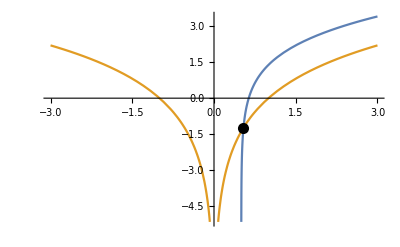

```mathematica
Plot[
{Log[2x-1]+Log[x+3],
Log[x^2]},
{x,-3,3},
Epilog->
	{
PointSize[0.02],Point[{0.5413812651491099,Log[0.5413812651491099^2]}]
}
]
```

```mathematica
Now
```

Tue 6 Oct 2020 09:01:10GMT-4.

```mathematica
Manipulate[
Plot[
{Log[b,2x-2]+Log[b,x+4],Log[b,3x^2]},
{x,-1,5},
PlotRange->{{-1,5},{-1,3}}
],
{{b,7},2,9,1}
]
```

```mathematica
Now
```

Thu 8 Oct 2020 10:50:36GMT-4.

How many divisors does any number have?

```mathematica
FactorInteger[720]
```

{{2,4},{3,2},{5,1}}

```mathematica
Length@Divisors[720]
```

30

```mathematica
5 3 2
```

30

```mathematica
2^4 5^3 13^2 19^4
```

44048498000

```mathematica
Length @ Divisors @ %
```

300

```mathematica
5 4 3 5
```

300

Write a function called staircaseNumbers[number, stairs] that take a number and “length of the staircase” and generates the appropriate list. For example, staircaseNumbers[15,5] would generate {1,2,3,4,5}. Similarly, staircaseNumbers[2020,5] would generate {402,403,404,405,406}. One more: staircaseNumbers[11,2] would give {5,6}.

```mathematica
staircaseNumbers[number_,stairs_]:=
Range[
number/stairs-(stairs-1)/2,(* starting number *)
number/stairs+(stairs-1)/2 (* ending number*)
]
staircaseNumbers[11,2]
```

{5,6}

```mathematica
staircaseNumbers[15,3]
```

{4,5,6}

```mathematica
staircaseNumbers[34,4]
```

{7,8,9,10}

```mathematica
Now
```

Fri 9 Oct 2020 13:33:43GMT-4.

```mathematica
Range[17,31]//Total
```

360

```mathematica
Range[70,74]//Total
```

360

```mathematica
Range[119,121]//Total
```

360

```mathematica
staircaseSets[360]
```

5

```mathematica
staircaseSets[total_]:=
Select[
Table[
staircaseNumbers[total,stairs],
{stairs,2,total}
],
AllTrue[#,IntegerQ]&& AllTrue[#,Positive]&
]//Length
```

```mathematica
staircaseSets[360]
```

5

```mathematica
staircaseSets2[n_]:=
Length[
Select[
Divisors[n],
OddQ[#]&
]
]-1
```

```mathematica
staircaseSets2[360]
```

5

```mathematica
staircaseSets2[2020]
```

3

```mathematica
Now
```

Fri 16 Oct 2020 08:46:55GMT-4.

```mathematica
180 ArcSin[8/17.]/Pi
```

28.0725

```mathematica
Now
```

Mon 19 Oct 2020 08:32:21GMT-4.

```mathematica
Grid
```

```mathematica
Manipulate[
Grid[
{

{
Labeled[
Graphics[
{
Thick, Circle[],
GrayLevel@.75, Disk[{0,0},1/5,{0,angle}],
Green,Line[{{0,0},{Cos[angle],Sin[angle]}}],
Red,Dashed,Line[{{Cos[angle],0},{Cos[angle],Sin[angle]}}],
Blue,Line[{{0,0},{Cos[angle],0}}],
Black,PointSize[0.05],Point[{Cos[angle],Sin[angle]}]
},
Axes->True,
Ticks->None,
ImageSize->{Automatic,200},
PlotRange->{{-1.1,1.1},{-1.1,1.1}}
],
{
Style[Cos[angle],Blue],
Style[Sin[angle],Red ]
}
],


Labeled[
Plot[
{
Sin[x],
Cos[x]
},
{x,0,angle},
PlotRange->{{0,6.5},{-1.1,1.1}},
Ticks-> {Range[0,2Pi,Pi/2],{-1,1}},
ImageSize->{Automatic,200},
PlotStyle->{{Red,Thick},{Blue,Thick}},
Epilog->{
Red,Opacity[1/2],Thick,Dashed,
Line[{{angle,0},{angle,Sin[angle]}}]
}
],
{
Style[{angle,Cos[angle]},Blue],
Style[{angle,Sin[angle]},Red]
}
]
},

{
Plot[
x^2,
{x,0,10},
ImageSize->{Automatic, 200}
]
}

}
],
{angle,0.001,2Pi}
]
```

```mathematica
Now
```

Tue 20 Oct 2020 10:51:33GMT-4.

```mathematica
TableForm[
Table[
{x,N[Sin[x Degree],4],N[Cos[x Degree],4],N[Tan[x Degree],4]},
{x,0,360,10}
],
TableHeadings->{None, {"angle","sine","cosine","tangent"}},
TableAlignments->Center
]
```

angle | sine | cosine | tangent
0 | 0 | 1. | 0
10 | 0.1736 | 0.9848 | 0.1763
20 | 0.342 | 0.9397 | 0.364
30 | 0.5 | 0.866 | 0.5774
40 | 0.6428 | 0.766 | 0.8391
50 | 0.766 | 0.6428 | 1.192
60 | 0.866 | 0.5 | 1.732
70 | 0.9397 | 0.342 | 2.747
80 | 0.9848 | 0.1736 | 5.671
90 | 1. | 0 | ComplexInfinity
100 | 0.9848 | -0.1736 | -5.671
110 | 0.9397 | -0.342 | -2.747
120 | 0.866 | -0.5 | -1.732
130 | 0.766 | -0.6428 | -1.192
140 | 0.6428 | -0.766 | -0.8391
150 | 0.5 | -0.866 | -0.5774
160 | 0.342 | -0.9397 | -0.364
170 | 0.1736 | -0.9848 | -0.1763
180 | 0 | -1. | 0
190 | -0.1736 | -0.9848 | 0.1763
200 | -0.342 | -0.9397 | 0.364
210 | -0.5 | -0.866 | 0.5774
220 | -0.6428 | -0.766 | 0.8391
230 | -0.766 | -0.6428 | 1.192
240 | -0.866 | -0.5 | 1.732
250 | -0.9397 | -0.342 | 2.747
260 | -0.9848 | -0.1736 | 5.671
270 | -1. | 0 | ComplexInfinity
280 | -0.9848 | 0.1736 | -5.671
290 | -0.9397 | 0.342 | -2.747
300 | -0.866 | 0.5 | -1.732
310 | -0.766 | 0.6428 | -1.192
320 | -0.6428 | 0.766 | -0.8391
330 | -0.5 | 0.866 | -0.5774
340 | -0.342 | 0.9397 | -0.364
350 | -0.1736 | 0.9848 | -0.1763
360 | 0 | 1. | 0

```mathematica
Now
```

Wed 21 Oct 2020 11:00:51GMT-4.

```mathematica
Table[
Sum[(-1)^n x^(2n)/(2n)!,{n,0,k,1}],
{k,0,4,1}
]
```

{1,1-x^2/2,1-x^2/2+x^4/24,1-x^2/2+x^4/24-x^6/720,1-x^2/2+x^4/24-x^6/720+x^8/40320}

```mathematica
Now
```

Fri 23 Oct 2020 13:54:59GMT-4.

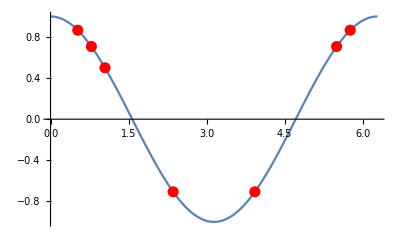

```mathematica
Plot[
Cos[x],{x,0,2Pi},
Epilog->{
PointSize@0.02,Red,
Point/@{{Pi/4,Sqrt[2]/2},{3Pi/4,-Sqrt[2]/2},{Pi/6,Sqrt[3]/2},{Pi/3,1/2}, {7Pi/4, Sqrt[2]/2},{5Pi/4,-Sqrt[2]/2},{11Pi/6,Sqrt[3]/2}}
}
]
```

```mathematica
Now
```

Mon 2 Nov 2020 11:00:24GMT-5.

EVERY SINGLE POINT on the unit circle has coordinates given by (cos t, sin t), where t is the angle that “generates” the point. So we can say the PARAMETRIC EQNS for the unit circle are 
x = cos t
y = sin t



```mathematica
ParametricPlot[
{Cos[t],Sin[t]},
{t,0,2Pi}
]
```

How do we find zeros of a transformed sine or cosine curve?

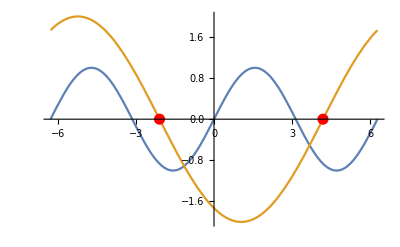

```mathematica
Plot[
{Sin[x],-2Sin[x/2+Pi/3]},
{x,-2Pi,2Pi},
Epilog->{
Red, PointSize[0.02],
Point[{{-2Pi/3,0},{4Pi/3,0}}]
}
]
```

we know that sin (anything) is zero when anything = ..., -2Pi, -Pi, 0Pi, Pi, ... 
sine is zero when its input is an integer multiple of pi

so in the case above, we need 
x/2 + pi/3 = 0 OR x/2 + pi/3 = pi OR x/2 + pi/3 = 2pi Or...
x = -2pi/3 Or x =

```mathematica
Now
```

Tue 3 Nov 2020 13:22:22GMT-5.

```mathematica
Manipulate[
Plot[
{Sin[b x],Sin[x]},
{x,-2Pi,2Pi},
PlotRange->{{-2Pi,2Pi},{-1.1,1.1}}
],
{b,1,7,1,Appearance->"Labeled"}
]
```

```mathematica
Now
```

Fri 13 Nov 2020 08:50:58GMT-5.

```mathematica
Plot[
{Sin[x],Cos[x]},
{x,0,2Pi}
]
```

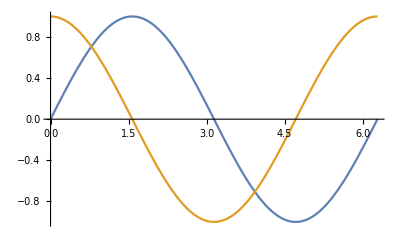

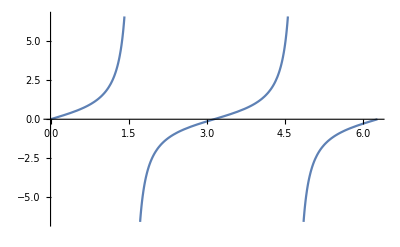

```mathematica
Plot[
Tan[x],
{x,0,2Pi}
]
```

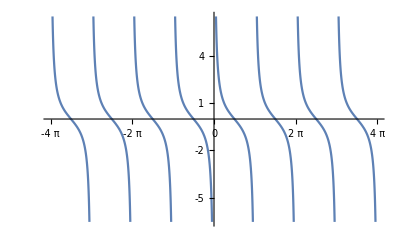

```mathematica
Plot[Cot[x],
{x,-4Pi,4Pi},
Ticks->{Range[-4Pi,4Pi,Pi],Range[-8,8,1]}
]
```

```mathematica
Now
```

Mon 16 Nov 2020 10:53:40GMT-5.

```mathematica
Manipulate[
Plot[
{Sin[x],Cos[x],Csc[x],Sec[x]},
{x,0,t},
Ticks->{Range[0,4Pi,Pi],Range[-5,5,2]},
PlotRange->{{0,4Pi},{-5,5}},
PlotStyle->{Blue,Red,Blue,Red},
Exclusions->{Cos[x]==0,Sin[x]==0}
],
{t,0.001,4Pi}
]
```

```mathematica
Manipulate[
Plot[
{Sin[x],Cos[x],Tan[x],Cot[x]},
{x,0,t},
Ticks->{Range[0,4Pi,Pi/2],Range[-5,5,2]},
PlotRange->{{0,4Pi},{-5,5}},
Exclusions->{Cos[x]==0,Sin[x]==0}
],
{t,0.001,4Pi}
]
```

```mathematica
Now
```

Wed 18 Nov 2020 13:32:58GMT-5.

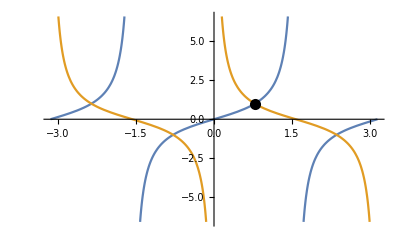

```mathematica
Plot[
{
Tan[x],Cot[x]
},
{x,-Pi,Pi},
Epilog ->{
PointSize[0.02],Point[{Pi/4,1}]
}
]
```

```mathematica
Now
```

Mon 23 Nov 2020 08:37:08GMT-5.

On the board in class, we just thought about the corners of a regular dodecagon. They all fit the patter {Cos[], Sin[]}

```mathematica
N@Table[
{Cos[2Pi n/10],Sin[2Pi n/10]},
(* n keeps track of which corner we're on *)
{n,1,10,1}
]
```

{{0.809017,0.587785},{0.309017,0.951057},{-0.309017,0.951057},{-0.809017,0.587785},{-1.,0.},{-0.809017,-0.587785},{-0.309017,-0.951057},{0.309017,-0.951057},{0.809017,-0.587785},{1.,0.}}

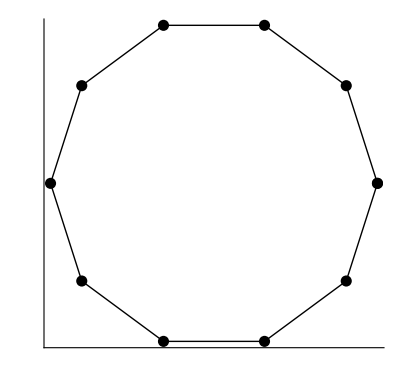

```mathematica
Graphics[
{
Line[{Table[{Cos[2Pi x/10],Sin[2Pi x/10]},{x,0,10,1}]}],
PointSize[0.02],
Point[
Table[{Cos[2Pi x/10],Sin[2Pi x/10]},{x,0,10,1}]
]
},
Axes->True,
Ticks->None
]
```

```mathematica
Subsets[{a,b,c,d},{2}]
```

{{a,b},{a,c},{a,d},{b,c},{b,d},{c,d}}

```mathematica
Now
```

Mon 30 Nov 2020 11:08:22GMT-5.

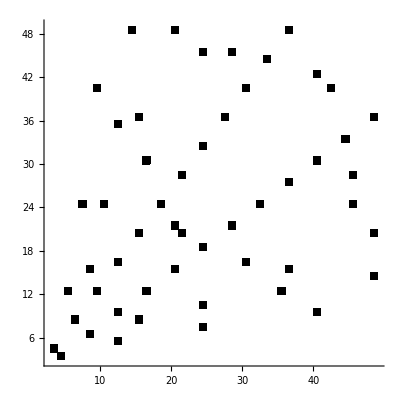

```mathematica
Graphics[
Table[
If[
IntegerQ[Sqrt[a^2+b^2]],
Rectangle[{a,b}]
],
{a,1,50,1},
{b,1,50,1}
],
Axes-> True,
AxesOrigin->{0,0}
]
```

The lines show the scaling up of the 3,4,5 and 4,3,5 triples. The other ones would create lines if the plot was bigger b/c they are spread out more.

```mathematica
Manipulate[
Graphics[
{
Red,InfiniteLine[{{0,0},{x,y}}],
Black,
Table[
If[
IntegerQ[Sqrt[a^2+b^2]],
Rectangle[{a,b}]
],
{a,1,100,1},
{b,1,100,1}
]
},
Axes-> True,
AxesOrigin->{0,0}
],
{x,3,40,1,Appearance->"Labeled"},
{y,3,40,1,Appearance->"Labeled"}
]
```

```mathematica
Now
```

Tue 1 Dec 2020 11:02:14GMT-5.

In class, we’re trying to figure out what (m,n) pairs generate primitive Pythagorean triples

```mathematica
Select[
Flatten[
Table[
{m,n,m^2-n^2,2m n,m^2+n^2},
{m,2,10,1},
{n,1,m-1,1}
],
1
],
GCD[#[[3]],#[[4]],#[[5]]]==1&
]
```

{{2,1,3,4,5},{3,2,5,12,13},{4,1,15,8,17},{4,3,7,24,25},{5,2,21,20,29},{5,4,9,40,41},{6,1,35,12,37},{6,5,11,60,61},{7,2,45,28,53},{7,4,33,56,65},{7,6,13,84,85},{8,1,63,16,65},{8,3,55,48,73},{8,5,39,80,89},{8,7,15,112,113},{9,2,77,36,85},{9,4,65,72,97},{9,8,17,144,145},{10,1,99,20,101},{10,3,91,60,109},{10,7,51,140,149},{10,9,19,180,181}}

```mathematica
Now
```

Thu 3 Dec 2020 13:20:27GMT-5.

From trig07 question 3: what fraction of (m,n) pairs generate primitive triples? Don’t forget that we’re starting with (m,n) pairs where m > n > 0. Here are some such pairs:

```mathematica
Flatten[
Table[
{m,n},
{m,2,6},
{n,1,m-1,1}
],
1
]
```

{{2,1},{3,1},{3,2},{4,1},{4,2},{4,3},{5,1},{5,2},{5,3},{5,4},{6,1},{6,2},{6,3},{6,4},{6,5}}

^ The number of possible pairs is always a triangular number. We only want these though:

```mathematica
Select[
Flatten[
Table[
{m,n},
{m,2,6},
{n,1,m-1,1}
],
1
],
OddQ[#[[1]]+#[[2]]] && GCD[#[[1]],#[[2]]]==1&
]
```

{{2,1},{3,2},{4,1},{4,3},{5,2},{5,4},{6,1},{6,5}}

```mathematica
Now
```

Tue 8 Dec 2020 08:41:58GMT-5.

On trig07 HW, what percentage of that particular image is black? white?

```mathematica
100 N @Length[
Select[
Flatten[
Table[
{m,n},
{m,2,6},
{n,1,m-1,1}
],
1
],
OddQ[#[[1]]+#[[2]]] && GCD[#[[1]],#[[2]]]==1&
]
]/(5 6/2)
```

53.3333

```mathematica
whatPercentPrimitive[k_]:=
100 N @Length[
Select[
Flatten[
Table[
{m,n},
{m,2,k},
{n,1,m-1,1}
],
1
],
OddQ[#[[1]]+#[[2]]] && GCD[#[[1]],#[[2]]]==1&
]
]/((k -1)k/2)
```

```mathematica
whatPercentPrimitive[1000]
```

40.6128

```mathematica
Table[{n,whatPercentPrimitive[n]},{n,50,500,50}]
```

{{50,42.2857},{100,41.2121},{150,41.0022},{200,40.9849},{250,40.8257},{300,40.7603},{350,40.7663},{400,40.7206},{450,40.678},{500,40.6934}}

```mathematica
Sum[1/n^2,{n,1,Infinity}]
```

π^2/6

```mathematica
Now
```

Fri 11 Dec 2020 10:52:19GMT-5.

Recall: here’s a log curve and an exponential curve on the same axes.

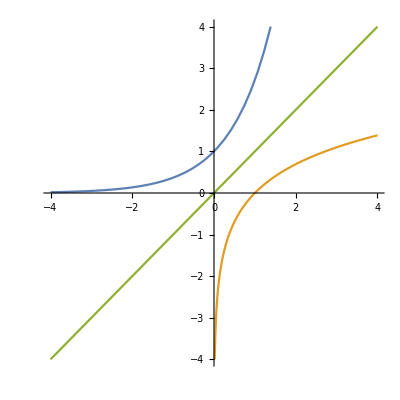

```mathematica
Plot[
{E^x,Log[x],x},
{x,-4,4},
PlotRange->{{-4,4},{-4,4}},
AspectRatio->1
]
```

These functions are reflections of each other across the line y = x. THEY ARE INVERSES OF EACH OTHER. The figure below shows a cosine curve.

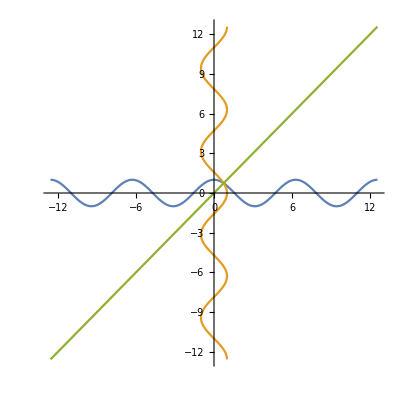

```mathematica
ParametricPlot[
{
{t,Cos[t]},
{Cos[t],t},
{t,t}
},
{t,-4Pi,4Pi},
{PlotRange->{{-4Pi,4Pi},{-4Pi,4Pi}}},
AspectRatio->1
]
```

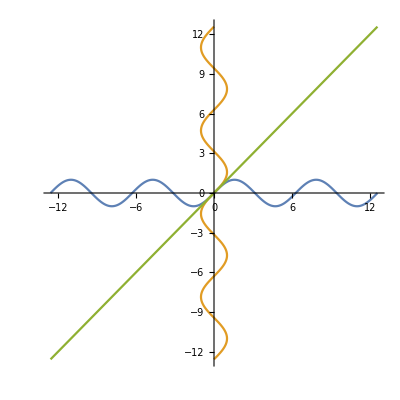

```mathematica
ParametricPlot[
{
{t,Sin[t]},
{Sin[t],t},
{t,t}
},
{t,-4Pi,4Pi},
{PlotRange->{{-4Pi,4Pi},{-4Pi,4Pi}}},
AspectRatio->1
]
```

```mathematica
Now
```

Mon 14 Dec 2020 13:20:33GMT-5.

In the previous parametric plot, the orange curve has equation x = sin y, but it’s not a function. On a calculator/Mathematica, however, the ArcSin[] or sin^(-1) function DOES behave as a function. For example, this command gives back a single output, not infinitely many outputs.

```mathematica
ArcSin[1/2]
```

π/6

In the command above, we are trying to find the angle whose sine ratio is 1/2. We could also perform computations like ArcSin[0.6801], ArcSin[0.3456], ArcSin[-0.22222222], BUT NOT ArcSin[3]. The point is: all inputs to ArcSin[] are real numbers between -1 and 1. Let’s generate LOTS of numbers between -1 and 1 and then find the angles that are associated with those values.

```mathematica
sineValues = RandomReal[{-1,1},12000];
```

```mathematica
angles = Map[180ArcSin[#]/Pi &,sineValues];
```

```mathematica
angles[[10001]]
```

35.4776

```mathematica
Max[angles]
```

88.7056

```mathematica
Min[angles]
```

-88.9184

The function ArcSin[] takes inputs between -1 and 1 and returns outputs between -Pi/2 and Pi/2. That should make sense, though, if we recall:

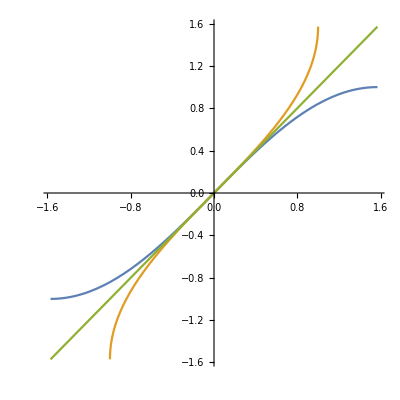

```mathematica
ParametricPlot[
{
{t,Sin[t]},
{Sin[t],t},
{t,t}
},
{t,-Pi/2,Pi/2},
{PlotRange->{{-Pi/2,Pi/2},{-Pi/2,Pi/2}}},
AspectRatio->1
]
```

```mathematica
Now
```

Tue 15 Dec 2020 13:42:30GMT-5.

We can have the same conversation about ArcCos[] we had about ArcSIn[]

In the previous parametric plot, the orange curve has equation x = cos y, but it’s not a function. On a calculator/Mathematica, however, the ArcCos[] or cos^(-1) function DOES behave as a function. For example, this command gives back a single output, not infinitely many outputs. So the Q is: how does ArcCos work?

```mathematica
ArcCos[1/2]
```

π/6

In the command above, we are trying to find the angle whose cosine ratio is 1/2. We could also perform computations like ArcCis[0.6801], ArcCos[0.3456], ArcCos[-0.22222222], BUT NOT ArcCos[3]. The point is: all inputs to ArcCos[] are real numbers between -1 and 1. Let’s generate LOTS of numbers between -1 and 1 and then find the angles that are associated with those values.

```mathematica
cosineValues = RandomReal[{-1,1},12000];
```

```mathematica
anglesC = Map[180ArcCos[#]/Pi &,cosineValues];
```

```mathematica
anglesC[[10001]]
```

84.6915

```mathematica
Max[anglesC]
```

179.381

```mathematica
Min[anglesC]
```

0.231001

The function ArCos[] takes inputs between -1 and 1 and returns outputs between 0 and Pi. That should make sense, though, if we recall:

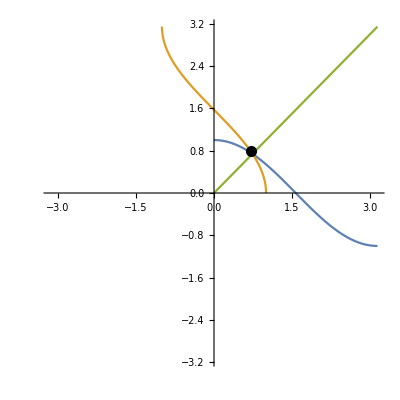

```mathematica
ParametricPlot[
{
{t,Cos[t]},
{Cos[t],t},
{t,t}
},
{t,0,Pi},
{PlotRange->{{-Pi,Pi},{-Pi,Pi}}},
AspectRatio->1,
Epilog->{
Black,PointSize[0.02],Point[{Sqrt[2]/2,Pi/4}]
}
]
```

The orange curve above now IS a function given by the eqn y = arccos(x), so the y-coord is the angle whose cosine value is given by the x-coord. That means (Sqrt[2]/2, Pi/4) is on the curve.

```mathematica
Plot[
{2Sin[x]^2-1,Sin[x]},
{x,-2Pi,2Pi},
Epilog-> {
PointSize[0.02],Point[Table[]]
}
]
```

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

-Graphics-

```mathematica
Now
```

Mon 4 Jan 2021 08:53:06GMT-5.

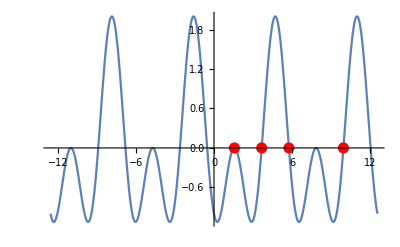

```mathematica
Plot[
{2Sin[x]^2-Sin[x]-1},
{x,-4Pi,4Pi},
Epilog->
{
Red,PointSize[0.02],Point[{#,0}]&/@{Pi/2,7Pi/6,11Pi/6,19Pi/6}
}
]
```

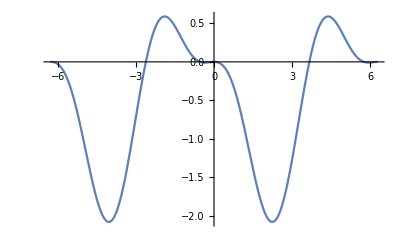

```mathematica
Plot[
(Sin[x]+1/2)(Cos[x]-1),
{x,-2Pi,2Pi}(* zeros not equally spread out *)
]
```

```mathematica
Now
```

Thu 14 Jan 2021 08:56:38GMT-5.

From our cosine chasing in class, we found

```mathematica
ChebyshevT[4,Cos[x]]
```

1-8 Cos[x]^2+8 Cos[x]^4

```mathematica
ChebyshevT[3,Cos[x]]
```

-3 Cos[x]+4 Cos[x]^3

```mathematica
TableForm[
Table[
{n,TraditionalForm@ChebyshevT[n,x]},
{n,0,10}
]
]
```

0 | 1
1 | x
2 | 2 x^2-1
3 | 4 x^3-3 x
4 | 8 x^4-8 x^2+1
5 | 16 x^5-20 x^3+5 x
6 | 32 x^6-48 x^4+18 x^2-1
7 | 64 x^7-112 x^5+56 x^3-7 x
8 | 128 x^8-256 x^6+160 x^4-32 x^2+1
9 | 256 x^9-576 x^7+432 x^5-120 x^3+9 x
10 | 512 x^10-1280 x^8+1120 x^6-400 x^4+50 x^2-1

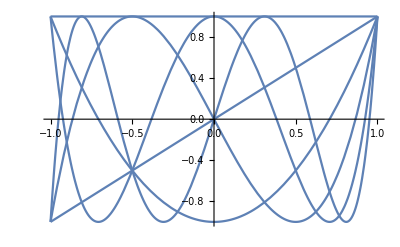

```mathematica
Plot[
Table[
ChebyshevT[n,x],
{n,0,5}
],
{x,-1,1}
]
```

promted by the HW, make a copy of the tri-in-the-rect figure for HW superTrig01.

```mathematica
Manipulate[
Graphics[
{
White,EdgeForm[Black],Rectangle[{0,0},{Sin[t+p],Cos[t]Cos[p]}],
Gray,Triangle[
{
{Sin[t]Cos[p],0},
{Sin[t+p],Cos[t]Cos[p]},
{0,Sin[t]Sin[p]}
}
]
}
],
{{p,Pi/6},0,Pi/3},
{{t,Pi/4},0,Pi/3}
]
```

```mathematica
Now
```

Fri 15 Jan 2021 10:57:17GMT-5.

Prompted by class notes, here’s a basic ParametricPlot[]

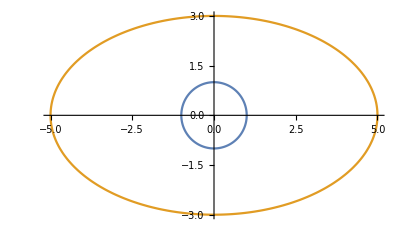

```mathematica
ParametricPlot[
{
{Cos[t],Sin[t]},
{5Cos[t],3Sin[t]}
},
{t,0,2Pi}
]
```

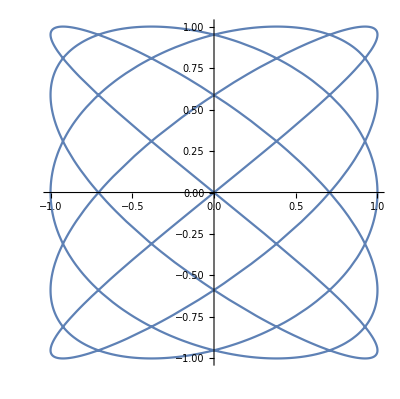

```mathematica
ParametricPlot[
{Sin[5t],Sin[4t]},
{t,0,2Pi}
]
```

The curve above could be generated by hand if you collected dozens of x values according to x = sin 5t and dozens of corresponding y values according to y = sin 4t, and then plot the ordered pairs. For example:

```mathematica
points = Table[
{Sin[5t],Sin[4t]},
{t,0,2Pi,0.1}
];
```

Every single point in the previous list is on the curve.

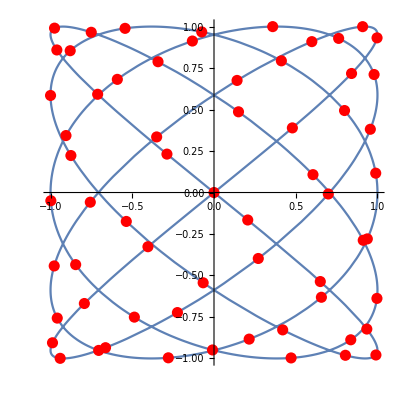

```mathematica
ParametricPlot[
{Sin[5t],Sin[4t]},
{t,0,2Pi},
Epilog->{
Red, PointSize[0.02], Point@points
}
]
```

```mathematica
TableForm[
Table[
Labeled[
ParametricPlot[
{Sin[a t],Sin[b t]},
{t,0,2Pi},
ImageSize->25,
Ticks->None
],
{}
],
{a,1,10},
{b,1,10}
]
]
```

-Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{}
-Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{}
-Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{}
-Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{}
-Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{}
-Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{}
-Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{}
-Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{}
-Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{}
-Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{} | -Graphics-{}